```mathematica
Needs["MaTeX`"]
```

## Effective Strong Measurements

### Binomial Model with Flat prior on p

```mathematica
$Assumptions=0<p<1&&n≥0&&0≤d≤n;
```

Define the prior, likelihood, and posterior distributions:

```mathematica
prior=BetaDistribution[1,1];
L=BinomialDistribution[n,p];
posterior=BetaDistribution[1+d,1+n-d];
```

This is the Fisher information of the likelihood:

```mathematica
J=Expectation[D[Log[PDF[L,d]],p]^2,d\[Distributed]L]//FullSimplify
```

n/(p-p^2)

```mathematica
Integrate[1/J,{p,0,1}]
```

1/(6 n)

This is the MSE of the Bayes estimator for p:

```mathematica
Expectation[(Mean[posterior]-p)^2,d\[Distributed]L]//FullSimplify
```

(1-(-4+n) (-1+p) p)/(2+n)^2

```mathematica
Expectation[Expectation[(Mean[posterior]-p)^2,d\[Distributed]L],p\[Distributed]prior]
```

1/(6 (2+n))

### Tricksy Method

```mathematica
$Assumptions=0<p<1&&0<β<α&&0<μα&&0<μβ&&0<σα&&0<σβ&&0<z&&0<x&&0<y&&n≥1&&λ>0;
```

Suppose we make m hypothetical measurements of Poisson(λ). Assuming a non-informative Gamma prior, we getting the following posterior, where x is the sum of the results:

```mathematica
hypPosterior=GammaDistribution[x,1/m]
```

GammaDistribution[x,1/m]

Now Let’s solve for the number of hypothetical experiments we need to do to achieve a posterior variance of σ^2, plugging in the MLE λ=x/m.

```mathematica
Solve[(Variance[hypPosterior]/.x->m λ)==σ^2,m]
```

{{m→λ/σ^2}}

```mathematica
ao=PoissonDistribution[m[λ]λ];
-Expectation[D[Log@PDF[ao,x],{λ,2}],x\[Distributed]ao]//FullSimplify
```

(m[λ]+λ m'[λ])^2/(λ m[λ])

```mathematica
DSolve[{(m[λ]+λ m'[λ])^2/(λ m[λ])==1/σ^2,m[0]==0},m[λ],λ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m[λ]→λ/(4 σ^2)}}

Now we set our data distribution to take 1 measurement of Poisson(p α+(1-p)β), and m measurements of Poisson(α) and Poisson(β):

```mathematica
dist=ProductDistribution[PoissonDistribution[α(α/σα^2/4+0)],PoissonDistribution[β(β/σβ^2/4+0)],PoissonDistribution[(β+p(α-β))]];
```

We would like the MSE under Bayes risk, as we did for the binomial model above. However, we settle for Fisher info since we can actually compute it.

```mathematica
logL=Log@PDF[dist,{x,y,z}]//FullSimplify//PowerExpand;
OI=-Outer[D[logL,#1,#2]&,{p,α,β},{p,α,β}]//FullSimplify;
Jintegrand=OI PDF[dist,{x,y,z}]//FullSimplify;
J=Sum[Jintegrand,{x,0,∞},{y,0,∞},{z,0,∞}];
```

Retrieve J_(p,p) as our quantity of interest.

```mathematica
invJ=Inverse[J]//FullSimplify;
invJ[[1,1]]
```

(β+σβ^2+p (α-β+p σα^2+(-2+p) σβ^2))/(α-β)^2

Recall that the fisher info of the raw Poisson model gives (J_(p,p))^-1=(p(α-β)+β)/(α-β)^2 and (J^-1)_(p,p)=(p (1+p) α+(-2+p) (-1+p) β)/(α-β)^2.
We see that our new formula, though complicated, correctly interpolates between them in the case of 1 measurements (m=1) and many prior measurements (m=∞).

```mathematica
Limit[Limit[invJ[[1,1]],σβ->Sqrt[β]],σα->Sqrt[α]]-(p (1+p) α+(-2+p) (-1+p) β)/(α-β)^2//FullSimplify
Limit[Limit[invJ[[1,1]],σβ->0],σα->0]-(p(α-β)+β)/(α-β)^2//FullSimplify
```

0

0

```mathematica
Integrate[invJ[[1,1]],{p,0,1}]//FullSimplify
```

(3 α+3 β+2 (σα^2+σβ^2))/(6 (α-β)^2)

```mathematica
esm[α_,β_,σα_,σβ_]=n/.First@Solve[(3 α+3 β+2 (σα^2+σβ^2))/(6 (α-β)^2)==1/(6n),n]//FullSimplify
```

(α-β)^2/(3 α+3 β+2 (σα^2+σβ^2))

```mathematica
Limit[Limit[esm[α,β,σα,σβ],σα->0],σβ->0]
Limit[Limit[esm[α,β,σα,σβ],σα->Sqrt[α]],σβ->Sqrt[β]]
```

(α-β)^2/(3 (α+β))

(α-β)^2/(5 (α+β))

### Comparison Plots

The following function computes (p-BE(p,z))^2, where BE(p,z) is the Bayes estimate of p given data value z.

```mathematica
mseCompiled=Compile[{z,μα,μβ,σα,σβ,p},
Module[{αs,βs,ps,nparticles=5000,weights,a},
αs=RandomVariate[NormalDistribution[μα,σα],nparticles];
βs=RandomVariate[NormalDistribution[μβ,σβ],nparticles];
ps=RandomReal[{0,1},nparticles];
weights=z Log[βs+ps(αs-βs)]-βs(1-ps)-αs ps;
a=Max[weights];
weights=weights-a-Log[Total[Exp[weights-a]]];
(Total[Exp[weights+Log[ps]]]-p)^2
]
];
```

This function draws a whole bunch of z to put into the above function.

```mathematica
generateData[μα_,μβ_,σα_,σβ_,p_,n_:1000]:=Module[{αs,βs},
αs=RandomVariate[NormalDistribution[μα,σα],n];
βs=RandomVariate[NormalDistribution[μβ,σβ],n];
RandomVariate[PoissonDistribution[p #1+(1-p)#2]]&@@@({αs,βs}ᵀ)
]
```

This is the composition of the above two functions.

```mathematica
mseFull[μα_,μβ_,σα_,σβ_,p_]:=Mean[mseCompiled[#,μα,μβ,σα,σβ,p]&/@generateData[μα,μβ,σα,σβ,p]]
```

Now we can generate data at a bunch of values of μα,μβ,σα,σβ,p:

```mathematica
makeCurves[μα_,μβ_,σα_,σβ_]:=makeCurves[μα,μβ,σα,σβ]=Module[{ps},
ps=Range[0,50]/50.;
{
{#,mseFull[μα,μβ,σα,σβ,#]}&/@ps,
With[{n=esm[μα,μβ,σα,σβ]//N},{ps,(1-(-4+n) (-1+ps) ps)/(2+n)^2}ᵀ]
}
]
```

```mathematica
Table[
makeCurves[μα,c μα,Sqrt[r μα],Sqrt[r c μα]],
{μα,{100,1000,10000}},
{r,{0.1,0.5,1}},
{c,{0.7}}
];
```

Finally, we struggle to plot it all in a grid:

```mathematica
(*See https://mathematica.stackexchange.com/a/6882/1167*)
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
mult[100]=0.15;
mult[1000]=0.025;
mult[10000]=0.0025;
```

```mathematica
title[μα_,r_,c_]:=MaTeX[#,Magnification->0.9]&/@With[{μβ=c μα,σα2=r μα,σβ2=r c μα},
{"\\alpha="<>ToString[Round[μα]]<>", \\beta="<>ToString[Round[μβ]]<>", \\sigma_\\alpha^2="<>ToString[Round[σα2]]<>", \\sigma_\\beta^2="<>ToString[Round[σβ2]],"\\text{ESM}="<>ToString[0.1*Round[10esm[μα,μβ,Sqrt@σα2,Sqrt@σβ2]]]}
]
```

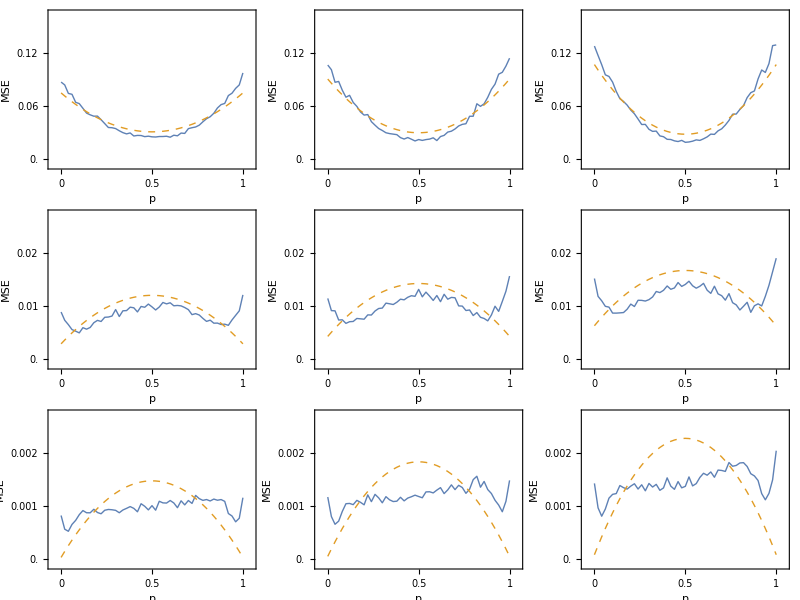

```mathematica
fig=With[{c=0.7},
plotGrid[
Table[
ListPlot[
makeCurves[μα,c μα,Sqrt[r μα],Sqrt[r c μα]],
Joined->True,
Frame->True,Axes->{True,False},
PlotRange->{{-0.05,1.05},{-0.05,1.1}mult[μα]},
FrameTicks->{{Range[0,mult[μα],mult[μα]/5],None},{{0,0.5,1},None}},
PlotStyle->{{Thick},{Thick,Dashed}},
FrameLabel->{"p","MSE"},
ImageSize->500,
BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->12},
Epilog->{Text[Style[title[μα,r,c][[1]]],Scaled[{0.99,0.99}],{1,1}],
Text[Style[title[μα,r,c][[2]],10],Scaled[{0.99,0.89}],{1,1}]}
],
{μα,{100,1000,10000}},
{r,{0.1,.5,1}}
],800,600,ImagePadding->75
]
];
SetDirectory[NotebookDirectory[]];
Export["../fig/effective-strong-meas.pdf",fig];
fig
```